```mathematica
Integrate[Sqrt[Cos[θ]^2],{θ,0,2π}]/(2π)
```

```mathematica
2/π//N
```

0.63662

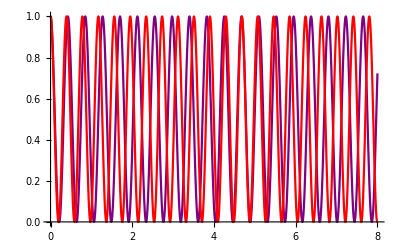

```mathematica
kLock = 2π/0.85;
kRyd = 2π/0.78;
Plot[{Cos[kLock z]^2,Cos[kRyd z]^2},{z,0,8},PlotStyle->{Purple,Red}]
```

```mathematica
kRyd*8/(2π)
```

10.2564

```mathematica
norm =Integrate[Cos[kLock z]^4,{z,0,kRyd*8}];
Integrate[Cos[kLock z]^2 Cos[kRyd z]^2,{z,0,kRyd*8}]/norm
```

0.664792

```mathematica
Table[Integrate[Cos[kLock z]^2 Cos[kRyd z+ϕ]^2,{z,0,kRyd*8}]/norm,{ϕ,Range[0,2π,2π/100]}]
```

{0.664792,0.663856,0.662965,0.662133,0.661374,0.660699,0.660119,0.659643,0.659278,0.659031,0.658906,0.658903,0.659024,0.659266,0.659626,0.660097,0.660674,0.661345,0.662101,0.66293,0.663819,0.664754,0.66572,0.666701,0.667683,0.668649,0.669586,0.670477,0.671308,0.672068,0.672743,0.673323,0.673799,0.674163,0.67441,0.674536,0.674539,0.674418,0.674176,0.673816,0.673344,0.672768,0.672097,0.67134,0.670511,0.669622,0.668688,0.667722,0.666741,0.665759,0.664792,0.663856,0.662965,0.662133,0.661374,0.660699,0.660119,0.659643,0.659278,0.659031,0.658906,0.658903,0.659024,0.659266,0.659626,0.660097,0.660674,0.661345,0.662101,0.66293,0.663819,0.664754,0.66572,0.666701,0.667683,0.668649,0.669586,0.670477,0.671308,0.672068,0.672743,0.673323,0.673799,0.674163,0.67441,0.674536,0.674539,0.674418,0.674176,0.673816,0.673344,0.672768,0.672097,0.67134,0.670511,0.669622,0.668688,0.667722,0.666741,0.665759,0.664792}

total overlap of the 850 and 780 intensities is not really dependent on the relative phase of the fields over this range